```mathematica
Elementary electromagnetism
Lihong Ao
2019271014
SZU,physics
```

```mathematica
第一章
E=1/(4π ϵ)(2q)/r^2=1/(4π ϵ)q/(L-r)^2   r=(√2)/(√2+1)L
```

```mathematica
Subscript[E, x](x,y)=q/(4π ϵ)((Cos π/4)/((x-Subscript[x, 0])+(y-Subscript[y, 0]))^2+(Cos (3π)/4)/((x-Subscript[x, 0])+(y+Subscript[y, 0]))^2+(Cos (5π)/4)/((x+Subscript[x, 0])+(y-Subscript[y, 0]))^2+(Cos (7π)/4)/((x+Subscript[x, 0])+(y+Subscript[y, 0]))^2)
Subscript[E, y](x,y)=q/(4π ϵ)((Sin π/4)/((x-Subscript[x, 0])+(y-Subscript[y, 0]))^2+(Sin (3π)/4)/((x-Subscript[x, 0])+(y+Subscript[y, 0]))^2+(Sin (5π)/4)/((x+Subscript[x, 0])+(y-Subscript[y, 0]))^2+(Sin (7π)/4)/((x+Subscript[x, 0])+(y+Subscript[y, 0]))^2)
Subscript[E, x](0,0)=Subscript[E, y](0,0)=0
```

```mathematica
Subscript[F, x]=1/(4π ϵ)(q/(2a)^2+q/(2 √2 a)^2 Cos π/4-Q/(√2 a)^2 Cos π/4)=0 
Q=1/4+1/(√2)
```

```mathematica
Subscript[E, x]=∫_Γ 1/(4π Subscript[ϵ, 0])(q/(2π R))/((r^(->)-x^(->))^2)r^(->)/(|r|)ⅆr=1/(8 π^2 R Subscript[ϵ, 0])∫_0^(2π) q/(R^2+x^2)x/(√(R^2+x^2))ⅆθ=(q x)/(4 π R (R^2+x^2)^(3/2) Subscript[ϵ, 0])
Subscript[E, r]=Subscript[E, θ]=0
E(x)=(0,0,(q x)/(4 π R (R^2+x^2)^(3/2) Subscript[ϵ, 0]))
```

```mathematica
(ⅆ Subscript[E, x])/ⅆx=(q (R^2-2 x^2))/(4 π R (R^2+x^2)^(5/2) Subscript[ϵ, 0])
q/(4 π R (R^2+x^2)^(5/2) Subscript[ϵ, 0])>0            R^2-2 x^2=0        x=R/(√2)
```

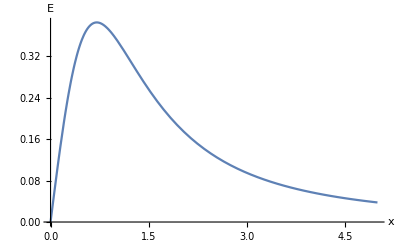

```mathematica
Plot[x/((1^2+x^2)^(3/2)),{x,0,5},AxesLabel->{x,"E"}]
```

```mathematica
Subscript[E, x]=∫_Γ 1/(4π Subscript[ϵ, 0])η/((r^(->)-x^(->))^2)r^(->)/(|r|)ⅆr=1/(2π Subscript[ϵ, 0])∫_0^(L/2) η/(l^2+R^2)x/(√(l^2+R^2))ⅆl=(η L)/(2 π R √(L^2+4 R^2) Subscript[ϵ, 0])
Underscript[Lim, L->∞] L/(√(L^2+4 R^2))=1                E|_(L->∞)=η/(2 π R Subscript[ϵ, 0])   
 (η L)/(2 π R √(L^2+4 R^2) Subscript[ϵ, 0])=(η L)/(4 π  Subscript[ϵ, 0] R^2)+O(2)^2=q/(4 π  Subscript[ϵ, 0] R^2)
```

```mathematica
∫_S EⅆS=2π R L|E|=(η L)/Subscript[ϵ, 0]
E=η/(2π R Subscript[ϵ, 0])
```

```mathematica
∫_S EⅆS=4π l^2|E|=(∫_0^l Subscript[ρ, 0](1-r/R)ⅆr-∫_l^R Subscript[ρ, 0](1-r/R)ⅆr)/Subscript[ϵ, 0],(0≤l≤R),(∫_0^R Subscript[ρ, 0](1-r/R)ⅆr)/Subscript[ϵ, 0],(l>R)
E=-((2 l^2-4 l R+R^2) Subscript[ρ, 0])/(8π R Subscript[ϵ, 0] l^2)(0≤l≤R),  (R Subscript[ρ, 0])/(2 Subscript[ϵ, 0] 4π l^2),(l>R)
ⅆE/ⅆl=((-2 l+R) Subscript[ρ, 0])/(4 l^3 π Subscript[ϵ, 0])     l=R/2
Subscript[E, max]=(7 Subscript[ρ, 0])/(4 π R Subscript[ϵ, 0])
```

```mathematica
W=∫_L^(3L) 1/(4π Subscript[ϵ, 0])q/r^2 ⅆr-0=q/(6 L π Subscript[ϵ, 0])
Subscript[W, 2]=∫_L^∞ 1/(4π Subscript[ϵ, 0])q/r^2 ⅆr-∫_(3L)^∞ 1/(4π Subscript[ϵ, 0])q/r^2 ⅆr=q/(6 L π Subscript[ϵ, 0])
```

```mathematica
∫_S EⅆS=4π r^2 E=0,(0≤r≤Subscript[R, 1]);Subscript[Q, 1]/Subscript[ϵ, 0](Subscript[R, 1]<r≤Subscript[R, 2]);(Subscript[Q, 1]+Subscript[Q, 2])/Subscript[ϵ, 0],(r>Subscript[R, 2])
E=0,(0≤r≤Subscript[R, 1]);Subscript[Q, 1]/(4π r^2 Subscript[ϵ, 0]),(Subscript[R, 1]<r≤Subscript[R, 2]);(Subscript[Q, 1]+Subscript[Q, 2])/(4π r^2 Subscript[ϵ, 0]),(r>Subscript[R, 2])
```

```mathematica
Subscript[E, 2]=0,(0≤r≤Subscript[R, 1]);Subscript[Q, 1]/(4π r^2 Subscript[ϵ, 0]),(Subscript[R, 1]<r≤Subscript[R, 2]);0,(r>Subscript[R, 2])
Subscript[E, 3]=0,(0≤r≤Subscript[R, 1]);Subscript[Q, 1]/(4π r^2 Subscript[ϵ, 0]),(Subscript[R, 1]<r≤Subscript[R, 2]);(Subscript[Q, 1](1-Subscript[R, 2]/Subscript[R, 1]))/(4π r^2 Subscript[ϵ, 0]),(r>Subscript[R, 2])
```

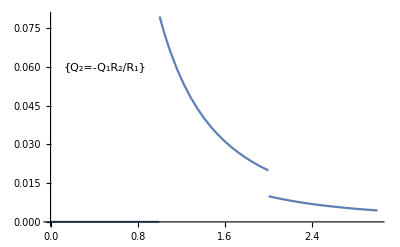

```mathematica
Plot[Piecewise[{{0,0≤r≤1},{1/(4π r^2),1<r≤2},{(1/2)/(4π r^2),r>2}}],{r,0,3},Epilog->Text[{"Q_2=-Q_1R_2/R_1"},{0.5,0.06}]]
```

```mathematica
第二章
```

```mathematica
∫_S EⅆS=4π r^2 E=q/ϵ=const
E=q/(4π ϵ r^2),(r∈(0,Subscript[R, 1])∪(Subscript[R, 2],∞));0,(r∈(Subscript[R, 1],Subscript[R, 2]))      U=-∫Eⅆr=q/(4π ϵ r)+Subscript[U, 0],(r∈(0,Subscript[R, 1]));-q/(4π ϵ Subscript[R, 1])+Subscript[U, 0],(r∈(Subscript[R, 1],Subscript[R, 2]));q/(4π ϵ (r-1))+Subscript[U, 0],(r∈(Subscript[R, 2],∞))
```

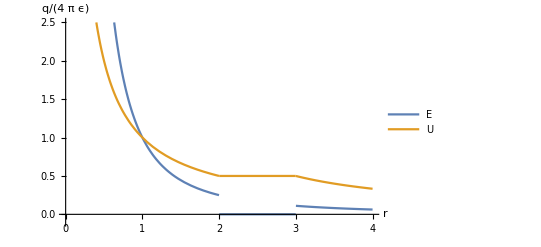

```mathematica
Plot[{Piecewise[{{1/r^2,0<r<2||r>3},{0,2<r<3}}],Piecewise[{{1/r,0<r<2},{1/2,2<r<3},{1/(r-1),r>3}}]},{r,0,4},PlotRange->{-.1,2.5},AxesLabel->{r,q/(4π ϵ)},PlotLegends->{"E",U}]
```

```mathematica
∫_(R=a) ρ/(4π ϵ a)ⅆS=-q/(4π ϵ a),∫_(R=b) ρ/(4π ϵ a)ⅆS=(Q+q)/(4π ϵ b)
U=Subscript[U, q]+Subscript[U, b]+Subscript[U, a]=q/(4π ϵ r)+(Q+q)/(4π ϵ b)+-q/(4π ϵ a)
Subscript[U, 2](0)=Subscript[U, 2](r)=∫_a^r Subscript[E, 2] ⅆR=(n q)/(4π ϵ)(a-r)/(a r)
U(0)=1/n Subscript[U, 2](0)=q/(4π ϵ)(a-r)/(a r)
```

```mathematica
∫_S EⅆS=2π r E=q/ϵ=const
E=k/r,U=k Log r+Subscript[U, 0]
k Log a+Subscript[U, 0]=Subscript[V, 1],k Log b+Subscript[U, 0]=Subscript[V, 2](k=const)
k->(Subscript[V, 1]-Subscript[V, 2])/(Log a-Log b),Subscript[U, 0]->(-Subscript[V, 1]Log b+Subscript[V, 2] Log a)/(Log a-Log b)
U=(Subscript[V, 1]-Subscript[V, 2])/(Log a-Log b) Log r+(-Subscript[V, 1]Log b+Subscript[V, 2] Log a)/(Log a-Log b),(a<r<b)
```

```mathematica
∫_S EⅆS=1/2(S U)/(d-t)=q/ϵ=const
∫_Subscript[S, 2] EⅆS=1/2(S U)/(d-t)=q/ϵ=const
C=q/U=(S ϵ)/(d-t)
C=d/(d-t)Subscript[C, 0]=4/3 Subscript[C, 0],U=q/C=10(V),Subscript[U, 0]=q/Subscript[C, 0]
Subscript[U, 0]=7.5(V)
```

```mathematica
U(r)=q/(4  π ϵ r),(r∈(Subscript[R, 2],∞))
U(r)=-α/r+Subscript[U, 0]      U(Subscript[R, 1])=0, U(Subscript[R, 2])=q/(4π ϵ Subscript[R, 2])
α=-(q Subscript[R, 1])/(4 π ϵ (Subscript[R, 1]+Subscript[R, 2])),Subscript[U, 0]=-q/(4 π ϵ (Subscript[R, 1]+Subscript[R, 2]))
```

```mathematica
Subscript[E, in]=(-Subscript[Q, 1])/(4π ϵ r^2),Subscript[E, out]=Subscript[Q, 2]/(4π ϵ r^2)
Subscript[U, 1]=∫_Subscript[R, 2]^∞ Subscript[E, out] ⅆr=Subscript[U, 2]=∫_Subscript[R, 1]^2 Subscript[E, in] ⅆr=(-Subscript[Q, 1])/(4π ϵ r^2)(1/Subscript[R, 1]-1/Subscript[R, 2])
Subscript[Q, 2]=(Subscript[R, 2]^2-Subscript[R, 1]^2)/Subscript[R, 2]^2 Subscript[Q, 1]
C=(Subscript[Q, 1]+Subscript[Q, 2])/Subscript[U, 1]=(4π ϵ Subscript[R, 2]^2)/(Subscript[R, 2]-Subscript[R, 1])
```

```mathematica
第三章
```

```mathematica
(S Subscript[σ, 0])/Subscript[ϵ, 0]=Subscript[Q, 0]/Subscript[ϵ, 0]=Subscript[E, 0] S,Subscript[U, 0]=Subscript[E, 0] l,Subscript[C, 0]=Subscript[Q, 0]/Subscript[U, 0]
Subscript[C, 0]=1.7708 *10^-10(F)
Subscript[q, 0]/Subscript[ϵ, 0]=Subscript[E, 0] S=Subscript[U, 0]/l S->Subscript[q, 0]=5.3124*10^-7(C)
C=Subscript[Q, 0]/U=Subscript[Q, 0]/(Subscript[U, 0]/3)=3 Subscript[C, 0]=5.3124*10^-10(F)
Subscript[E, 0]=Subscript[U, 0]/l=3*10^5(V/m)
E=U/l=10^5(V/m)
(|q'|)/Subscript[ϵ, 0]=(Subscript[U, 0]-U)/l S->|q'|=3.5416*10^-7(C)
D=Subscript[q, 0]/S=Subscript[ϵ, 0] Subscript[ϵ, r] Subscript[E, 0]->Subscript[ϵ, r]=3
```

```mathematica
(d Subscript[ϵ, r]-t)E+t Subscript[ϵ, r] E=U->E=U/(Subscript[ϵ, r] d-t(1-Subscript[ϵ, r])),
D=Subscript[ϵ, 0] Subscript[ϵ, r] E=(Subscript[ϵ, 0] Subscript[ϵ, r] U)/(Subscript[ϵ, r] d-t(1-Subscript[ϵ, r])),P=Subscript[ϵ, 0] χ E=Subscript[ϵ, 0](Subscript[ϵ, r]-1)E=(Subscript[ϵ, 0](Subscript[ϵ, r]-1)U)/(Subscript[ϵ, r] d-t(1-Subscript[ϵ, r]))
Subscript[q, 0]=D S=(Subscript[ϵ, 0] Subscript[ϵ, r] U S)/(Subscript[ϵ, r] d-t(1-Subscript[ϵ, r])),Subscript[E, 空]=Subscript[ϵ, r] E=(Subscript[ϵ, r] U)/(Subscript[ϵ, r] d-t(1-Subscript[ϵ, r])),C=Subscript[q, 0]/U=(Subscript[ϵ, 0] Subscript[ϵ, r] S)/(Subscript[ϵ, r] d-t(1-Subscript[ϵ, r]))
```

```mathematica
Subscript[λ, 0]=2π r D=2π r Subscript[ϵ, 0] Subscript[ϵ, r] E
E=Subscript[λ, 0]/(2π r Subscript[ϵ, 0] Subscript[ϵ, r]),D=Subscript[ϵ, 0] Subscript[ϵ, r] E=(Subscript[λ, 0] Subscript[ϵ, 0] Subscript[ϵ, r])/(2π r Subscript[ϵ, 0] Subscript[ϵ, r]),P=Subscript[ϵ, 0](Subscript[ϵ, r]-1)E=(Subscript[λ, 0](Subscript[ϵ, r]-1))/(2π r Subscript[ϵ, r])
U=∫_Subscript[R, 1]^Subscript[R, 2] Eⅆr=Subscript[λ, 0]/(2π Subscript[ϵ, 0] Subscript[ϵ, r])ln Subscript[R, 2]/Subscript[R, 1]
σ'S=-P S->σ'=-P=Subscript[ϵ, 0](Subscript[ϵ, r]-1)E|_(r=Subscript[R, 2])=((Subscript[ϵ, r]-1)Subscript[λ, 0])/(2π Subscript[R, 2] Subscript[ϵ, r])
```

```mathematica
Subscript[W, e]=(C U^2)/2->W'/W=C'/C(U'/U)^2=Subscript[ϵ, 0]/ϵ(U'/U)^2
d E'=Subscript[ϵ, r] d E=U->E'/E=Subscript[ϵ, r]
Subscript[ϵ, 0]/ϵ=1/5,U'/U=1->W'/W=1/5
Subscript[ϵ, 0]/ϵ=1/5,U'/U=E'/E=1/Subscript[ϵ, r]->W'/W=5
```

```mathematica
Subscript[q, 0] =4π r^2 D=4π r^2 ϵ E->E=Subscript[q, 0]/(4π r^2 ϵ)
w=(ϵ E^2)/2=Subscript[q, 0]^2/(32 π^2 r^4 ϵ)
```

```mathematica
第四章
```

```mathematica
2 Subscript[i, 1] Subscript[R, 1]=ϵ,(Subscript[R, 1]+Subscript[R, 0])Subscript[i, 0]+(Subscript[i, 0]-Subscript[i, 1])Subscript[R, 1]=0,Subscript[i, 1]=ϵ/Subscript[R, 0]->Subscript[R, 1]=Subscript[R, 0]/2
```

```mathematica
R=∫_0^L ρ/(S(r))ⅆr,S(r)=π(a+(b-a)/L r)^2->R=(L ρ)/(a b π)
a=b=√(S/π)->R=(ρ L)/S
```

```mathematica
i=(Subscript[ϵ, 1]+Subscript[ϵ, 2])/(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3])=2(A)
Subscript[U, AB]=Subscript[ϵ, 1]-Subscript[R, 1] i=0
Subscript[U, AC]=Subscript[ϵ, 1]+Subscript[ϵ, 2]-(Subscript[R, 1]+Subscript[R, 2])i=8(V)
Subscript[U, CB]=-Subscript[ϵ, 2]+Subscript[R, 2] i=-8(V)
```

```mathematica
Subscript[U, E]=-Subscript[ϵ, 1],Subscript[U, D]=Subscript[ϵ, 2],Subscript[U, B]=Subscript[ϵ, 3]
Subscript[U, A]=Subscript[U, D]-Subscript[R, 2] Subscript[i, A]=Subscript[ϵ, 2]-Subscript[ϵ, 2]/(Subscript[R, 2]+Subscript[R, 4])Subscript[R, 2]
```

```mathematica
Subscript[i, 2] Subscript[R, 2]+Subscript[i, 3] Subscript[R, 3]=Subscript[ϵ, 2],Subscript[i, 1] Subscript[R, 1]-Subscript[R, 3] Subscript[i, 3]=Subscript[ϵ, 1],Subscript[i, 1]+Subscript[i, 3]=Subscript[i, 2]
Subscript[R, 2]=(-Subscript[i, 2] Subscript[R, 1] Subscript[R, 3]+Subscript[R, 1] Subscript[ϵ, 2]+Subscript[R, 3] (Subscript[ϵ, 1]+Subscript[ϵ, 2]))/(Subscript[i, 2] (Subscript[R, 1]+Subscript[R, 3])),Subscript[i, 1]=(Subscript[i, 2] Subscript[R, 3]+Subscript[ϵ, 1])/(Subscript[R, 1]+Subscript[R, 3]),Subscript[i, 3]=(Subscript[i, 2] Subscript[R, 1]-Subscript[ϵ, 1])/(Subscript[R, 1]+Subscript[R, 3])
```

```mathematica
ϵ=24;Subscript[R, 1]=80;Subscript[R, 2]=240;Subscript[R, 3]=Subscript[R, 5]=120;Subscript[i, 4]=0.125;
Subscript[i, 2] Subscript[R, 1]-Subscript[i, 1] Subscript[R, 2]+(Subscript[i, 4]-Subscript[i, 1])Subscript[R, 5]=0,(Subscript[i, 2]-Subscript[i, 4]+Subscript[i, 1])Subscript[R, 3]-Subscript[i, 4] Subscript[R, 4]-Subscript[R, 5](Subscript[i, 4]-Subscript[i, 1])=0,Subscript[i, 4] Subscript[R, 4]+Subscript[i, 1] Subscript[R, 2]=ϵ
Subscript[i, 1]=0.075(A),Subscript[i, 2]=0.15(A),Subscript[R, 4]=48(Ω)
```

```mathematica
6+2=Subscript[i, 1](r+2+2),-6=Subscript[i, 2](r+2+6),r=R//3//6,-2 Subscript[i, 2]=-2 Subscript[i, 1]+2
Subscript[i, 1]=1/2(A),Subscript[i, 2]=-1/2(A),R=18/7(Ω)





第五章
```

```mathematica
Subscript[B, a]=Subscript[μ, 0]/(4π)∫_Γ (i r^(->))/(|r^3|)ⅆl=(3 Subscript[μ, 0])/8 i/R+∫_0^∞ (i R)/((R^2+x^2)^(3/2))ⅆx=(1+(3 Subscript[μ, 0])/(8 R))i
Subscript[B, b]=Subscript[μ, 0]/4 i/R+∫_0^∞ (i R)/((R^2+x^2)^(3/2))ⅆx+∫_0^∞ (-i R)/((R^2+x^2)^(3/2))ⅆx=Subscript[μ, 0]/4 i/R
```

```mathematica
Subscript[B, a]=(3 Subscript[μ, 0])/8 i/a+Subscript[μ, 0]/8 i/b=(Subscript[μ, 0] i)/8(3/a+1/b)
Subscript[B, b]=(3 Subscript[μ, 0])/8 i/a+2∫_0^b (i R)/((b^2+x^2)^(3/2))ⅆx=(√2  i R)/b^2+(3 i Subscript[μ, 0])/(8 a)
```

```mathematica
<AOC=(1-a)/(2π)       ρ,R
ρ a R Subscript[i, 1]=ρ(1-a)Subscript[Ri, 2],Subscript[i, 1]+Subscript[i, 2]=i
Subscript[i, 1]=(1-a)i,Subscript[i, 2]=a i
Subscript[B, o]=Subscript[μ, 0]/(4π)((3π)/4 a i+π/4(1-a)i)=1/16 (i+2 a i) Subscript[μ, 0]
```

```mathematica
Subscript[B, P]=4∫_0^a ∫_0^∞ Subscript[μ, 0]/(4π)(i x)/((r^2+l^2+x^2)^(3/2))ⅆlⅆr= (Subscript[μ, 0] i)/π ArcTan a/x
```

```mathematica
B=Subscript[μ, 0]/(4π)∫_h ∫_Γ (i r^(->))/(|r^3|)ⅆlⅆh=2 Subscript[μ, 0]/(4π)∫_0^R 2π R(σ ω √(R^2-h^2)h)/R^3 ⅆh=1/3 R σ ω Subscript[μ, 0]
```

```mathematica
2π r B(r)=Subscript[μ, 0] i->B(r)=(Subscript[μ, 0] i)/(2π r)
Φ=l ∫_a^b B(r)ⅆr=(i l (-ln a+ln b) Subscript[μ, 0])/(2 π)
```

```mathematica
2 r a J Subscript[μ, 0]=B(r) a->B(r)=2 r J Subscript[μ, 0],(r≤d)
2 d  a J Subscript[μ, 0]=B(r) a->B(r)=2 d J Subscript[μ, 0](r>d)
```

```mathematica
2π Subscript[r, 1] Subscript[B, 1]=π r^2 i->Subscript[B, 1]=(Subscript[r, 1] i)/2=i/2 √(x^2+y^2),Subscript[B, 1x]=i/2 x,Subscript[B, 1y]=i/2 y(Subscript[r, 1]<a)

2π Subscript[r, 2] Subscript[B, 2]=π Subscript[r, 2]^2 i->Subscript[B, 2]=(Subscript[r, 2] i)/2=i/2 √((x-c)^2+y^2)(Subscript[r, 2]≤b),Subscript[B, 2]=(b i)/2(Subscript[r, 2]>b),
Subscript[B, 2x]=i/2(x-c),Subscript[B, 2y]=i/2 y
2π Subscript[r, 1] B=π(a^2-b^2)i->B=((a^2-b^2)i)/(2π Subscript[r, 1])(Subscript[r, 1]>a)
Subscript[B, x]=Subscript[B, 1x]-Subscript[B, 2x]=(i c)/2,Subscript[B, y]=Subscript[B, 1y]-Subscript[B, 2y]=0(Subscript[r, 2]<b)
Subscript[B, x]=1/2 i (x+(b (c-x))/(√((c-x)^2+y^2))),Subscript[B, y]=(i y)/2-(b i y)/(2 √((c-x)^2+y^2))(Subscript[r, 2]>b&&Subscript[r, 1]<a)
Subscript[B, x]=((a^2-b^2)i)/(2π Subscript[r, 1])x/(√(x^2+y^2)),Subscript[b, y]=((a^2-b^2)i)/(2π Subscript[r, 1])y/(√(x^2+y^2))(Subscript[r, 1]>a)
```

```mathematica
Subscript[B, 0]=Subscript[μ, 0]/(4π)∫_0^π ∫_(-∞)^∞ (i/π R)/((R^2+x^2)^(3/2))ⅆxⅆθ=Subscript[μ, 0]/(4π)∫_(-∞)^∞ (i R)/((R^2+x^2)^(3/2))ⅆx=(i Subscript[μ, 0])/(2 π R)
F=Subscript[i B, 0]=(i^2 Subscript[μ, 0])/(2 π R)
Subscript[B, 1]=Subscript[μ, 0]/(4π)∫_(-∞)^∞ (i r)/((r^2+x^2)^(3/2))ⅆx=Subscript[μ, 0]/(4π)∫_(-∞)^∞ (i R)/((R^2+x^2)^(3/2))ⅆx=Subscript[B, 0]->r=R
```

```mathematica
Subscript[F, 1]=-2i B R
Subscript[F, 2]=2 B i Cos θ Cos φ=2 B i x/R Cos φ,x=R Cos θ
Subscript[F, 1] Subscript[r, 0]+∫_0^Subscript[r, 0] Subscript[F, 2] ⅆx=-∫_Subscript[r, 0]^R Subscript[F, 2] ⅆx->Subscript[r, 0]=1/3 R Cos φ,M=2∫_Subscript[r, 0]^R Subscript[F, 2] ⅆx=-4/3 B i R Cos θ(-3+Cos φ) Cos φ
Subscript[p, m]=M/B=-4/3 i R Cos θ(-3+Cos φ) Cos φ
```

```mathematica
第六章
```

```mathematica
B=Subscript[μ, 0] n i,Subscript[E, i]=-r/2 ⅆB/ⅆt,Subscript[ϵ, i]=2π Subscript[n, 2] r Subscript[E, i]
Subscript[ϵ, i]=-π Subscript[μ, 0] n Subscript[n, 2] r^2 ⅆi/ⅆt=4.8 π^2*10^-5(V)
```

```mathematica
Subscript[ϵ, PQ]=∫_Subscript[Γ, PQ] v^(->)*B^(->)ⅆl=∫_0^r ω r B Sin θ ⅆr/(Sin θ)=∫_0^r ω r Bⅆr=1/2 B r^2 ω
```

```mathematica
Subscript[ϵ, PQ]=Subscript[v, 1]^(->)*B^(->) l=8(V),Subscript[ϵ, MN]=Subscript[v, 2]^(->)*B^(->) l=4(V)
i=(|Subscript[ϵ, PQ]|-|Subscript[ϵ, MN]|)/(2R),Subscript[U, PQ]=Subscript[ϵ, PQ]-i R=6(V),Subscript[U, MN]=-Subscript[ϵ, MN]-i R=6(V)
Subscript[U, O1]-Subscript[U, O2]=6V
```

```mathematica
Subscript[ϵ, AM]=∫_Subscript[Γ, AM] v^(->)*B^(->)ⅆl=∫_0^(R/(√2)) ω r Bⅆr=1/4 B R^2 ω,Subscript[ϵ, AC]=∫_0^R ω r Bⅆr=1/2 B R^2 ω
```

```mathematica
Subscript[U, c]>Subscript[U, M]>Subscript[U, A]
```

```mathematica
Subscript[ϵ, ON]=Subscript[ϵ, OM]=Subscript[ϵ, OP]=Subscript[ϵ, OQ]=0
Subscript[ϵ, MN]=(-ⅆ Subscript[Φ, OMN])/ⅆt=25/16 √3*10^-6(V),Subscript[ϵ, PQ]=(-ⅆ Subscript[Φ, OPQ])/ⅆt=25/4 √3*10^-6(V)
```

```mathematica
B=(Subscript[μ, 0] i)/(2π r)(r∈(Subscript[R, 1],Subscript[R, 2]))
Φ=∫BⅆS=∫_Subscript[R, 1]^Subscript[R, 2] B lⅆr=∫_Subscript[R, 1]^Subscript[R, 2] (Subscript[μ, 0] i)/(2π r) lⅆr=(Subscript[μ, 0] i l)/(2π)(ln Subscript[R, 2])/(ln Subscript[R, 1])
```

```mathematica
Subscript[i, 1] R+i R=ϵ,i R=ϵ-L(ⅆ Subscript[i, 2])/ⅆt,Subscript[i, 1] R=-L(ⅆ Subscript[i, 2])/ⅆt,i=Subscript[i, 1]+Subscript[i, 2]
i|_(t=0)=0
i=(ϵ(1-ⅇ^(-(R t)/(2 L))))/R,Subscript[i, 1]=(ⅇ^(-(R t)/(2 L)) ϵ)/R,Subscript[i, 2]=(ϵ(1-2 ⅇ^(-(R t)/(2 L))))/R
```

```mathematica
Subscript[u, c]=Subscript[R, 2]/(Subscript[R, 1]+Subscript[R, 2])ϵ+c∫Subscript[i, c] ⅆt,Subscript[i, c] Subscript[R, 1]=ϵ-Subscript[u, c]
Subscript[u, c]|_(t=0)=Subscript[R, 2]/(Subscript[R, 1]+Subscript[R, 2])ϵ
Subscript[i, c]=(ⅇ^(-(c t)/Subscript[R, 1]) ϵ)/(Subscript[R, 1]+Subscript[R, 2]),Subscript[u, c]=ϵ-(ⅇ^(-(c t)/Subscript[R, 1]) ϵ Subscript[R, 1])/(Subscript[R, 1]+Subscript[R, 2])          Subscript[u, c]|_(t=2τ)=ϵ-(ⅇ^(-(2c τ)/Subscript[R, 1]) ϵ Subscript[R, 1])/(Subscript[R, 1]+Subscript[R, 2])  
Subscript[u, c∞]=ϵ
W=(c Subscript[u, c∞]^2)/2=(c ϵ^2)/2
```

```mathematica
Quit[]
```

ClearAll